```mathematica
SetDirectory["/media/alexander/9e1069d5-cd39-4e83-8eff-49b4335462dd/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/LIF_Logic/feedforward_temp"]
fileList=FileNames["*"];
Length[fileList]
(*Step 3:Extract the indices and read the files into an Association*)
Monitor[
table=Table[Import["e_"<>IntegerString[e,10,3]<>"_i_"<>IntegerString[i,10,3]<>"_k_"<>IntegerString[k,10,3],"Table"][[2;;-1,1]],{e,0,23},{i,0,15},{k,0,4}];
(*Use the tableList*)
Dimensions[tableList],{e,i,k}]
```

/media/alexander/9e1069d5-cd39-4e83-8eff-49b4335462dd/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/LIF_Logic/feedforward_temp

1920

Import::nffil: File e_016_i_000_k_000 not found during Import.

Part::take: Cannot take positions 2 through -1 in $Failed.

Import::nffil: File e_016_i_000_k_001 not found during Import.

Part::take: Cannot take positions 2 through -1 in $Failed.

Import::nffil: File e_016_i_000_k_002 not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::take: Cannot take positions 2 through -1 in $Failed.

General::stop: Further output of Part::take will be suppressed during this calculation.

{}

```mathematica
{If[data[[2,2,60]]>20,1,0],If[data[[2,2,140]]>20,1,0],If[data[[2,2,220]]>20,1,0]}
```

```mathematica
{1,1,1}
```

{1,1,1}

```mathematica
isGate[data_,thresh_]:=Block[{seg},
seg={If[data[[140]]>thresh,1,0],If[data[[300]]>thresh,1,0],If[data[[460]]>20,1,0],If[data[[600]]>thresh,1,0]};
Piecewise[{
{1,seg=={1,1,1,1}},
{2,seg=={1,1,1,0}},
{3,seg=={0,1,1,0}},
{4,seg=={1,0,0,0}},
{5,seg=={0,1,1,1}},
{6,seg=={1,0,0,1}},
{7,seg=={0,0,0,1}},
{8,seg=={0,0,0,0}}
}]
]
tot =23
dat=Table[isGate[table[[i,j,k]],1],{i,1,15},{j,1,tot},{k,1,5}];
```

11

0.65

RGBColor[0.8, 0.1, 0.1]

RGBColor[0.9, 0.5, 0.2]

RGBColor[0.9, 0.8, 0.3]

RGBColor[0.1, 0.8, 0.4]

RGBColor[0.1, 0.4, 0.8]

RGBColor[0.7, 0.4, 0.8]

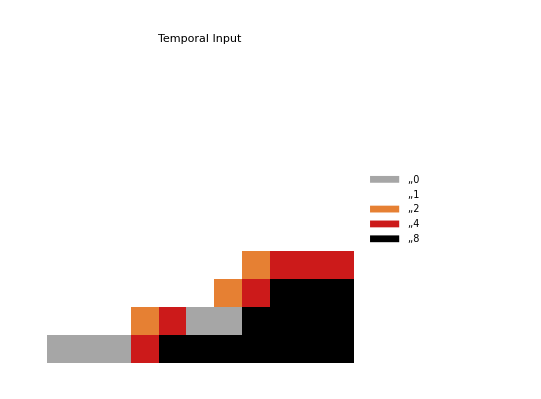
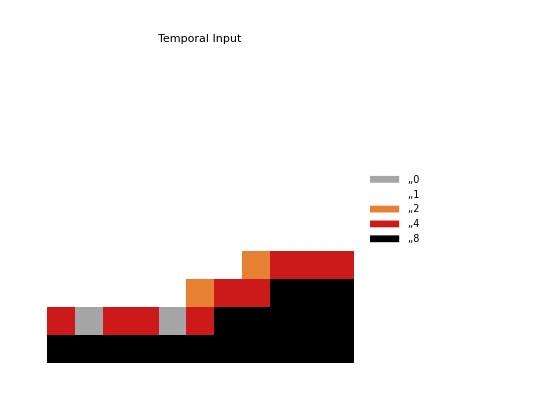
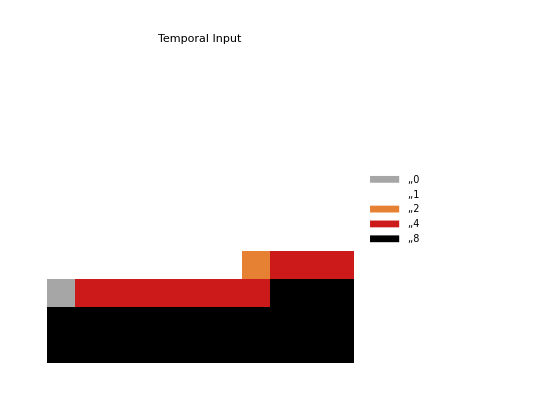
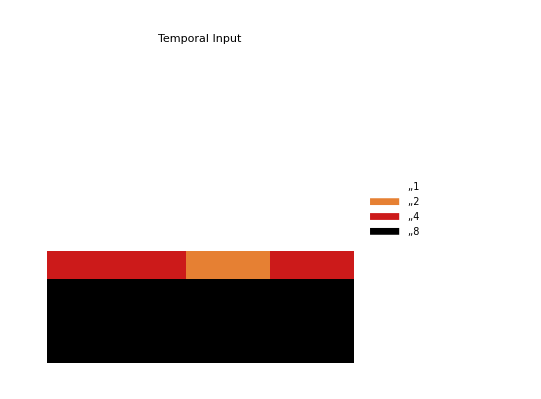
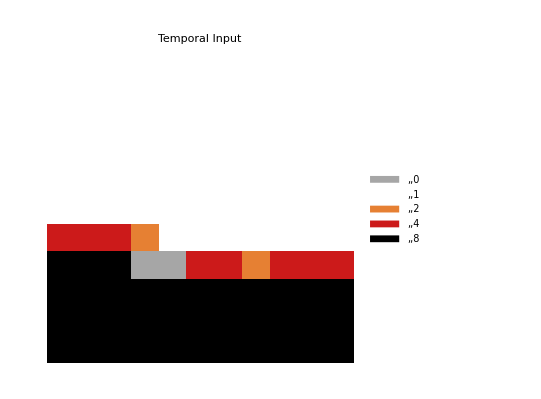
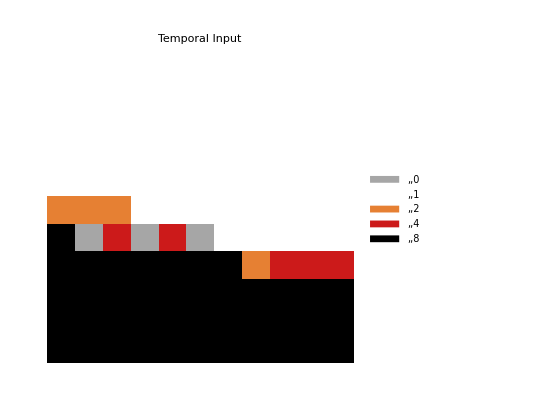
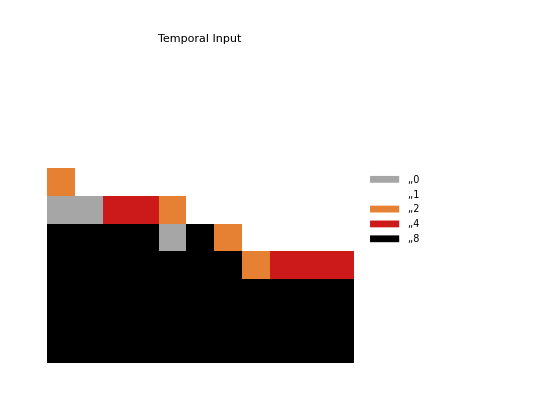
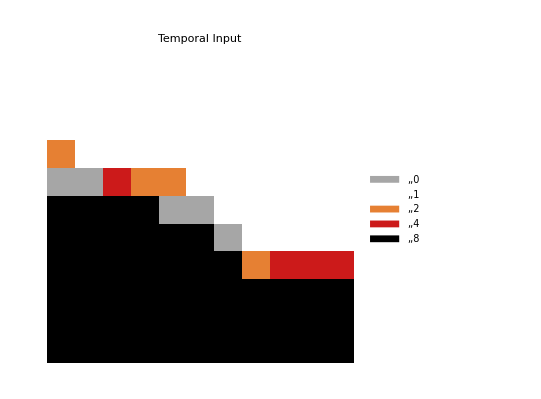

```mathematica
grey=.65
red = RGBColor[.8,.1,.1]
orange=  RGBColor[.9,.5,.2]
yellow=RGBColor[.9,.8,.3]
green= RGBColor[.1,.8,.4]
blue =RGBColor[.1,.4,.8]
purple=RGBColor[.7,.4,.8]

Table[
ArrayPlot[Reverse[dat[[All,All;;-1,k]],{1,2}],ColorRules->
{8->Black,1->White,4->red,2->orange,3->yellow,5->green,7->blue,6->purple,0->GrayLevel[grey],"NIMP1"->GrayLevel[grey],"NIMP2"->GrayLevel[grey],"AIMP1"->GrayLevel[grey],"AIMP2"->GrayLevel[grey],"XIMP1"->GrayLevel[grey],"XIMP2"->GrayLevel[grey],"IMP1"->GrayLevel[grey],"IMP2"->GrayLevel[grey]},PlotLegends->Automatic,DataRange->{{1.5,4.5},{-2.5,0.5}},FrameTicks->Automatic,FrameLabel->{"Input Bias","Hidden Bias"},PlotLabel->Style["Temporal Input","Title",Black,20]],{k,1,9}]
```

```mathematica
sS
```

```mathematica
Dimensions[table]
```

{16,16,20,151}

```mathematica
dat=Table[isGate[table[[i,j,k]],1],{i,1,tot},{j,1,tot},{k,1,7}]
```

Part::partw: Part 6 of {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«640»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«640»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«640»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«640»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«640»}} does not exist.

Part::partw: Part 140 of {{{{0., 0., <<647>>, 0.}, <<4>>}, <<23>>}, <<15>>}[[1,1,6]] does not exist.

Part::partw: Part 300 of {{{{0., 0., <<647>>, 0.}, <<4>>}, <<23>>}, <<15>>}[[1,1,6]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
i=1
j=1
k=1
isGate[table[[i,j,k]],1]
```

1

1

1

8

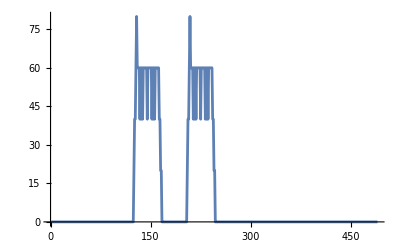

```mathematica
ListLinePlot[table[[4,4,9]]]
```

```mathematica
Position[dat[[All,All,9]],3]
```

{{4,4}}

/media/alexander/9e1069d5-cd39-4e83-8eff-49b4335462dd/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/LIF_Logic/feedforward_temp_V

5

5

0

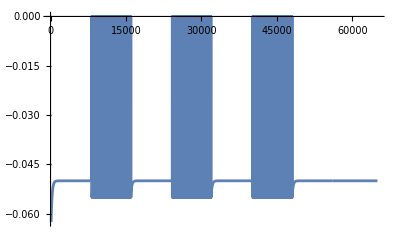

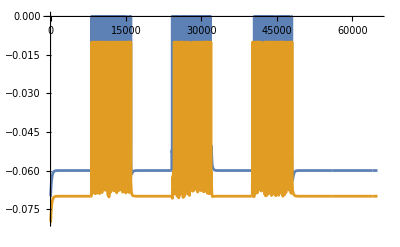

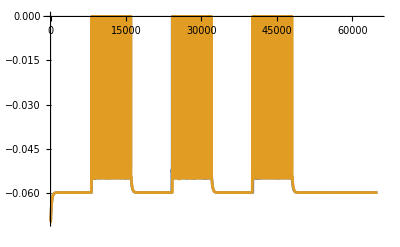

```mathematica
SetDirectory["/media/alexander/9e1069d5-cd39-4e83-8eff-49b4335462dd/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/LIF_Logic/feedforward_temp_V"]
fileList=FileNames["*"];
e=5
i =5
k =0
vdat=Import["V_e_"<>IntegerString[e,10,3]<>"_i_"<>IntegerString[i,10,3]<>"_k_"<>IntegerString[k,10,3],"Table"][[2;;-1,1]];

ve=Import["Ve_e_"<>IntegerString[e,10,3]<>"_i_"<>IntegerString[i,10,3]<>"_k_"<>IntegerString[k,10,3],"Table"][[2;;-1,1]];

vi=Import["Vi_e_"<>IntegerString[e,10,3]<>"_i_"<>IntegerString[i,10,3]<>"_k_"<>IntegerString[k,10,3],"Table"][[2;;-1,1]];
ve2=Import["Ve2_e_"<>IntegerString[e,10,3]<>"_i_"<>IntegerString[i,10,3]<>"_k_"<>IntegerString[k,10,3],"Table"][[2;;-1,1]];

vi2=Import["Vi2_e_"<>IntegerString[e,10,3]<>"_i_"<>IntegerString[i,10,3]<>"_k_"<>IntegerString[k,10,3],"Table"][[2;;-1,1]];
ListLinePlot[vdat]
ListLinePlot[{ve,ve2-.01}]
ListLinePlot[{vi,vi2}]
```

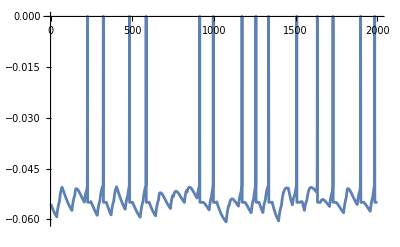

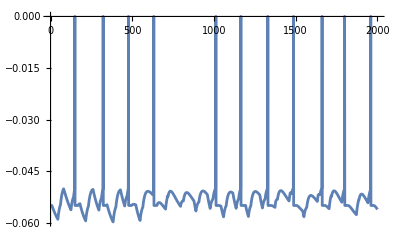

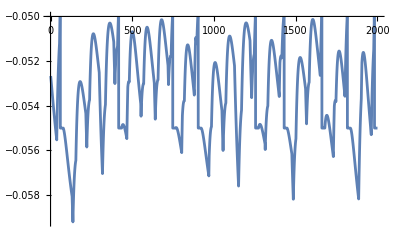

```mathematica
ListLinePlot[ve[[10000;;12000]]]
ListLinePlot[ve[[25000;;27000]]]
ListLinePlot[ve[[45000;;47000]],PlotRange->{All,-.05}]
```